```mathematica
dat52 = Import["/Users/daria/ThinFilmEllipsometryLinear2DModel/data/Gr_AOI_52.dat","Data"];
dat052 = Import["/Users/daria/ThinFilmEllipsometryLinear2DModel/data/Without_Gr_AOI_52.dat","Data"];
prepdat52 = dat52⟦5;;,All⟧;
psidat52 = prepdat52[[All,3]];
deltadat52 = prepdat52[[All,4]];
prepdat052 = dat052⟦5;;,All⟧;
psidat052 = prepdat052[[All,3]];
deltadat052 = prepdat052[[All,4]];
diffpsidat52 = psidat52-psidat052;
diffdeltadat52=deltadat52-deltadat052;
lambda = prepdat52⟦All,1⟧;
k = 2 π/lambda;(* nm^-1 *)
```

```mathematica
TableForm@diffdeltadat52⟦1;; 7⟧
```

-0.94551
-0.84499
-0.91858
-0.99134
-0.995
-0.91142
-0.95668

```mathematica
Print[diffdeltadat52⟦1⟧," " ,diffpsidat52⟦1⟧]
```

-0.94551 0.19484

```mathematica
ϕ=52/360 2π;
d = 0.35; (* nm *)
n=1.5; (* glass *)
G[ϵ_]:=-2 I k⟦1⟧d ((n^2-Sin[ϕ]^2)/(n^4-n^2+Sin[ϕ]^2) (ϵ^2-ϵ+Sin[ϕ]^2)/ϵ - (ϵ-Sin[ϕ]^2-1)/(n^2-Sin[ϕ]^2-1));
sols = {};
For[i=1, i<=233,i++,
AppendTo[sols,NSolve[G[ϵ]==diffpsidat52⟦i⟧/(Cos[psidat052⟦i⟧]*Sin[psidat052⟦i⟧])+I diffdeltadat52⟦i⟧,ϵ]⟦1⟧⟦1⟧⟦2⟧ ]];
```

```mathematica
NSolve[G[ϵ]==diffpsidat52⟦1⟧/(Cos[psidat052⟦1⟧]*Sin[psidat052⟦1⟧])+I diffdeltadat52⟦1⟧,ϵ]
```

{{ϵ→-68.472-117.72 ⅈ},{ϵ→0.000975303-0.00167678 ⅈ}}

```mathematica
NSolve[{nn^2-kk^2==Re[sols]⟦2⟧,2 nn kk == Im[sols]⟦2⟧},{nn,kk},Reals]⟦1⟧
```

{nn→2.80264,kk→-8.29752}

```mathematica
OptN={};
OptK={};
For[i=1, i<=233,i++,
AppendTo[OptN, NSolve[{nn^2-kk^2==Re[sols]⟦i⟧,2 nn kk == Im[sols]⟦i⟧},{nn,kk},Reals]⟦1⟧⟦1⟧⟦2⟧];
AppendTo[OptK, NSolve[{nn^2-kk^2==Re[sols]⟦i⟧,2 nn kk == Im[sols]⟦i⟧},{nn,kk},Reals]⟦1⟧⟦2⟧⟦2⟧];
];
```

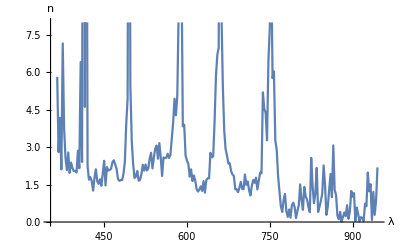

```mathematica
ListLinePlot[Transpose[{lambda,Abs@OptN}],PlotRange->{All,{0,8}},AxesLabel->{λ,HoldForm@n}]
```